```mathematica
Quit[]
```

```mathematica
(*Constant parameters*)
ssthw=0.23116;
gpV=0.5-2*ssthw;
gnV=-0.5;
hbar=197.327;(*MeV.fm*)
GF = 1.166378*10^-5;(*GeV^-2*)
Na=6.022*10^23;(*Avogadro nunber*)
Mamu=931.494; (*MeV atomic mass unit*)

(*pion decay at rest*)
Mpi=139.57018 ;(*MeV*)
Mmu=105.6583715; (*MeV*)
Enumu=(Mpi^2-Mmu^2)/(2*Mpi);

(*Neutrino Energy distribution*)
Fnumubar[Enu_](*MeV^-1*):=
Module[{res},
If[Enu>Mmu/2,res=0,
res=(64/Mmu)*(Enu/Mmu)^2*(3/4-Enu/Mmu);];
res
];
Fnue[Enu_](*MeV^-1*):=
Module[{res},
If[Enu>Mmu/2,res=0,
res=(192/Mmu)*(Enu/Mmu)^2*(1/2-Enu/Mmu);];
res
];

(*Energy range*)
(*Neutrino energy range in MeV*)
(*Subscript[ν, μ]*)
Enumu=(Mpi^2-Mmu^2)/(2*Mpi);
(*Subscript[ν̄, μ]*)
Enumubarmax=Mmu/2;
EnumubarminF[MNuc_,Er_]:=√(MNuc*Er/2);
(*Subscript[ν, e]*)
Enuemax=Mmu/2;
EnueminF[MNuc_,Er_]:=√(MNuc*Er/2);
(*Recoil energy range for each kind of neutrino in MeV*)
(*Subscript[ν, μ]*)
ErnumumaxF[MNuc_]:=2*Enumu^2/MNuc;
Ernumumin=0.;
(*Subscript[ν̄, μ]*)
ErnumubarmaxF[MNuc_]:=2*Enumubarmax^2/MNuc;
Ernumubarmin=0.;
(*Subscript[ν, e]*)
ErnuemaxF[MNuc_]:=2*Enuemax^2/MNuc;
Ernuemin=0.;

(*Helm FF*)
R0HelmF[Rrms_,s_]:=Sqrt[5.0/3.0*(Rrms^2-3*s^2)];
HelmF[Q_,R0_,s_]:=3/(Q*R0/hbar)*(Sin[Q*R0/hbar]/(Q*R0/hbar)^2-Cos[Q*R0/hbar]/(Q*R0/hbar))*Exp[-(Q*R0/hbar)^2*s^2/R0^2/2];
FF[Q_,Rrms_,s_]:=HelmF[Q,R0HelmF[Rrms,s],s]
```

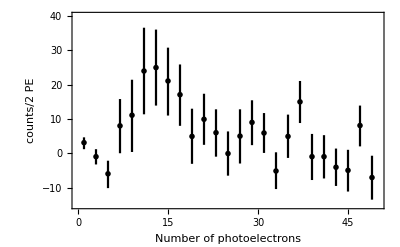

{3.14516,-0.9375,-5.92742,8.04435,11.129,24.0121,25.0101,21.1089,17.1169,4.95968,9.9496,6.04839,-0.0302419,5.0504,9.04234}

{1.72379,2.22278,3.99194,7.89315,10.5242,12.6109,11.0685,9.88911,8.93649,8.02923,7.43952,6.89516,6.44153,7.89315,6.53226}

```mathematica
(*Surviving fraction*)
(*Use 1804.09459*)
acca=0.6655;
acck=0.4942;
accx0=10.8507;
acctheta[x_]:=Module[{res},
If[x<5,res=0,
If[x≥6,res=1,res=0.5]];
res
]
accF[x_]:=acca/(1+Exp[-acck*(x-accx0)])*acctheta[x];
p2=Plot[accF[x],{x,0,50},PlotStyle->Red];
(*Data point 1708.01294*)
datapointM={{0.999231360492,3.14516129032},{0.999231360492,1.23991935484},{0.999231360492,4.6875},{2.99769408148,-0.9375},{2.99769408148,-3.20564516129},{2.99769408148,1.23991935484},{4.99615680246,-5.92741935484},{4.99615680246,-10.1008064516},{5.03458877786,-2.11693548387},{6.99461952344,8.04435483871},{6.99461952344,0.0604838709677},{6.99461952344,15.8467741935},{8.99308224443,11.1290322581},{9.03151421983,0.423387096774},{8.99308224443,21.4717741935},{10.9915449654,24.0120967742},{11.0299769408,11.4012096774},{11.0299769408,36.623},{13.0284396618,25.0100806452},{13.0284396618,13.9415322581},{12.9900076864,36.0786},{15.0269023828,21.1088709677},{15.0269023828,11.0383064516},{15.0269023828,30.8165322581},{16.9869331284,17.1169354839},{17.0253651038,8.04435483871},{17.0253651038,25.9173387097},{18.9853958493,4.95967741935},{19.0238278248,-3.02419354839},{19.0238278248,13.0342741935},{20.9838585703,9.94959677419},{21.0222905457,2.51008064516},{21.0222905457,17.3891129032},{22.9823212913,6.04838709677},{23.0207532667,-0.9375},{23.0207532667,12.8528225806},{25.0192159877,-0.0302419354839},{25.0192159877,-6.47177419355},{25.0192159877,6.41129032258},{27.0176787087,5.05040322581},{27.0176787087,-2.93346774194},{27.0176787087,12.8528225806},{29.0161414297,9.04233870968},{29.0161414297,2.41935483871},{29.0161414297,15.4838709677},{31.0146041507,5.95766129032},{31.0530361261,0.151209677419},{31.0146041507,11.7641129032},{33.0130668716,-5.11088709677},{33.0130668716,-10.372983871},{33.0130668716,0.332661290323},{35.0115295926,4.95967741935},{35.0115295926,-1.30040322581},{35.0115295926,11.310483871},{36.9715603382,15.0302419355},{37.0099923136,8.86088709677},{37.0099923136,21.1088709677},{39.0084550346,-0.9375},{39.0084550346,-7.74193548387},{39.0084550346,5.68548387097},{41.0069177556,-0.9375},{41.0069177556,-7.28830645161},{41.0069177556,5.32258064516},{43.0053804766,-4.02217741935},{43.0053804766,-9.46572580645},{43.0053804766,1.42137096774},{45.0038431975,-4.92943548387},{45.0038431975,-11.0987903226},{45.0038431975,1.05846774194},{47.0023059185,8.13508064516},{47.0023059185,2.0564516129},{47.0023059185,13.9415322581},{49.0007686395,-7.01612903226},{49.0007686395,-13.4576612903},{49.0007686395,-0.665322580645}};

(*Prompt neutrons*)
rawdataM={{0.5,0.5526297688},{1.5,0.3600910306},{2.5,0.2893956006},{3.5,0.2455627024},{4.5,0.2146807015},{5.5,0.1870733798},{6.5,0.1672490835},{7.5,0.1485182494},{8.5,0.1309850961},{9.5,0.1176154017},{10.5,0.1059512645},{11.5,0.09618978202},{12.5,0.08857161552},{13.5,0.0814935416},{14.5,0.07583297789},{15.5,0.07025010884},{16.5,0.06572848558},{17.5,0.06062696502},{18.5,0.05677618831},{19.5,0.05254071578},{20.5,0.04883775488},{21.5,0.04655988514},{22.5,0.04468566552},{23.5,0.04201362282},{24.5,0.03922787309},{25.5,0.03755453229},{26.5,0.03586792201},{27.5,0.03401644155},{28.5,0.03259514272},{29.5,0.03017514199},{30.5,0.02954977006},{31.5,0.02846010774},{32.5,0.02676591836},{33.5,0.02588471211},{34.5,0.02438192442},{35.5,0.02406544797},{36.5,0.02307243273},{37.5,0.02263846248},{38.5,0.02197708562},{39.5,0.02133844793},{40.5,0.02100870572},{41.5,0.02059747651},{42.5,0.01988303661},{43.5,0.01959309168},{44.5,0.01897908933},{45.5,0.01875547133},{46.5,0.01815663092},{47.5,0.01761464216},{48.5,0.01659699157},{49.5,0.01667658426}};
promptneutronM={};plotM={};
For[i=1,i<=Length[rawdataM]/2,i++,
temp=(rawdataM[[2*i-1,2]]*accF[rawdataM[[2*i-1,1]]]+rawdataM[[2*i,2]]*accF[rawdataM[[2*i,1]]])*7.47594;
promptneutronM=Join[promptneutronM,{{rawdataM[[2*i-1,1]]+0.5,temp}}];
plotM=Join[plotM,{{rawdataM[[2*i-1,1]]-0.5,temp},{rawdataM[[2*i,1]]+0.5,temp}}];(*multiply by the acceptance efficiency*)
];

(* Old Quench factor sigmaalpha=0.28*)
ErF[PE_]:=PE/1.17;
dErdPE[x_]:=1/1.17;

Needs["ErrorBarPlots`"]
centerM=Table[{2*(i-1)+1,datapointM[[(i-1)*3+1,2]]},{i,1,Length[datapointM]/3}];
errorM=Table[{datapointM[[(i-1)*3+2,2]]-datapointM[[(i-1)*3+1,2]],datapointM[[(i-1)*3+3,2]]-datapointM[[(i-1)*3+1,2]]},{i,1,Length[datapointM]/3}];
coherentdataM=Table[{centerM[[i]],ErrorBar[errorM[[i]]]},{i,1,Length[centerM]}];
Pdata=ErrorListPlot[coherentdataM,PlotRange->{{0,50},{-15,40}},Frame->True,BaseStyle->FontSize->16,PlotStyle->{Black,PointSize[0.01]},FrameLabel->{"Number of photoelectrons","counts/2 PE"}]

dataM=Table[centerM[[i,2]],{i,1,15}]
uncertaintyM=Table[(-errorM[[i,1]]+errorM[[i,2]])/2,{i,1,15}]
```

```mathematica
dsigmadErF[ZNuc_,NNuc_,MNuc_,Er_,Enu_,Rprms_,Rnrms_,s_]:=(* 10^(-38)cm^2/MeV*)
Module[{QwI,res},
QwI=-2*(ZNuc*gpV*FF[Sqrt[2*MNuc*Er],Rprms,s]+NNuc*gnV*FF[Sqrt[2*MNuc*Er],Rnrms,s]);
res=GF^2/(2*Pi)*MNuc*(2-MNuc*Er/(Enu^2))*hbar^2*(QwI^2/4);
res
];

dNnumudErF[ZNuc_,NNuc_,MNuc_,Er_,Rprms_,Rnrms_,s_]:=
Module[{temp,Ernumumax},
Ernumumax=ErnumumaxF[MNuc];
temp=If[Er<Ernumumax,dsigmadErF[ZNuc,NNuc,MNuc,Er,Enumu,Rprms,Rnrms,s],0];
temp
];

dNnumubardErF[ZNuc_,NNuc_,MNuc_,Er_,Rprms_,Rnrms_,s_]:=
Module[{sum,step=10,ix,x,h,temp,Enumubarmin,Ernumubarmax},
sum=0;
Enumubarmin=EnumubarminF[MNuc,Er];
Ernumubarmax=ErnumubarmaxF[MNuc];
If[Er<Ernumubarmax,
(*Integrate over Enumubar*)
h=(Enumubarmax-Enumubarmin)/step;
For[ix=0,ix<step,ix++,
x=Enumubarmin+ix*h;
sum=sum+Fnumubar[x+h/2.0]*dsigmadErF[ZNuc,NNuc,MNuc,Er,x+h/2.0,Rprms,Rnrms,s]*h;
];
];
sum
];

dNnuedErF[ZNuc_,NNuc_,MNuc_,Er_,Rprms_,Rnrms_,s_]:=
Module[{sum,step=10,ix,x,h,temp,Enuemin,Ernuemax},
sum=0;
Enuemin=EnueminF[MNuc,Er];
Ernuemax=ErnuemaxF[MNuc];
If[Er<Ernuemax,
(*Integrate over Enuebar*)
h=(Enuemax-Enuemin)/step;
For[ix=0,ix<step,ix++,
x=Enuemin+ix*h;
sum=sum+Fnue[x+h/2.0]*dsigmadErF[ZNuc,NNuc,MNuc,Er,x+h/2.0,Rprms,Rnrms,s]*h;
];
];
sum
];
```

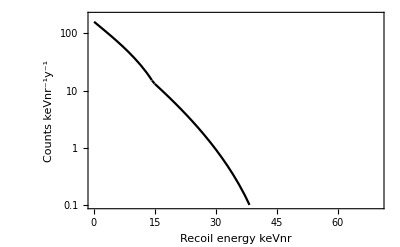

```mathematica
dNdErMF[ErkeV_,nucleusM_,Nnu_,NTtotal_,s_]:= (*Er MeV*)
Module[{sum=0,ErMeV,inuc,ZZ,NN,abundance,Rpexp,Rnth},
ErMeV=ErkeV/1000;
For[inuc=1,inuc<=Length[nucleusM],inuc++,
ZZ=nucleusM[[inuc,1]];
NN=nucleusM[[inuc,2]];
abundance= nucleusM[[inuc,3]];
Rpexp= nucleusM[[inuc,4]];
Rnth=nucleusM[[inuc,5]];
sum=sum+ abundance*(dNnuedErF[ZZ,NN,(ZZ+NN)*Mamu,ErMeV,Rpexp,Rnth,s]+dNnumudErF[ZZ,NN,(ZZ+NN)*Mamu,ErMeV,Rpexp,Rnth,s]+dNnumubardErF[ZZ,NN,(ZZ+NN)*Mamu,ErMeV,Rpexp,Rnth,s]);
];
sum*10^(-38)*Nnu*NTtotal/1000
]

(*Number of neutrinos per cm^2 per 308.1 liveday *)
L=1930;(*cm*)
Nnu=1.76*10^23*(308.1/308.1)*0.08/(4*Pi*L^2);
(*Total Number of target nucleus*)
mdet=14.6;(*kg*)
nucleusM={{55, 78, 0.5, 4.804, 5.01},{53,74,0.5, 4.750,4.94}};(*Z, N, abundance, Rp experiment, Rn theory*)
Mave=Module[{i,res=0},
For [i=1,i≤Length[nucleusM],i++,
res=res+(nucleusM[[i,1]]+nucleusM[[i,2]])*nucleusM[[i,3]];
];
res
];(*Average molar mass*)
NTtotal=mdet*1000/Mave*Na;
s=0.9;(*fm*)
P0=LogPlot[dNdErMF[ErkeV,nucleusM,Nnu,NTtotal,s],{ErkeV,0.1,70},PlotRange->{{0,70},{0.1,200}},Frame->True,PlotStyle->{{Black}},BaseStyle->FontSize->16,Axes->None,FrameLabel->{"Recoil energy keVnr","Counts keVnr^-1y^-1"}]
```

22

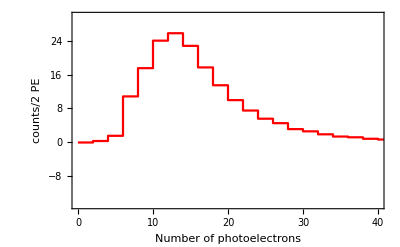

```mathematica
nueM={{0.975,-0.11811023622},{3,0.236220472441},{5.025,1.47637795276},{6.975,10.8661417323},{9,17.5984251969},{10.95,24.1535433071},{12.975,25.9251968504},{15,22.9133858268},{16.95,17.7755905512},{18.975,13.5236220472},{20.925,9.98031496063},{22.95,7.5},{24.975,5.55118110236},{27,4.48818897638},{29.025,3.07086614173},{31.05,2.53937007874},{32.925,1.83070866142},{34.8,1.29921259843},{36.975,1.12204724409},{39,0.767716535433},{40.95,0.590551181102},{42.975,0.590551181102}};
Length[nueM]
nueplotM={};
For[i=1,i<=Length[nueM],i++,
nueplotM=Join[nueplotM,{{2*i-2,nueM[[i,2]]}}];
nueplotM=Join[nueplotM,{{2*i,nueM[[i,2]]}}];
];


pnue0=ListPlot[nueplotM,Joined->True,PlotRange->{{0,40},{-15,30}},Frame->True,BaseStyle->FontSize->16,Axes->None,PlotStyle->{Red},FrameLabel->{"Number of photoelectrons","counts/2 PE"}]
```

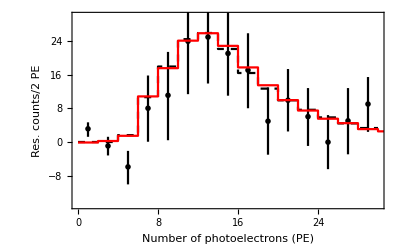

```mathematica
dNdPEMF[PE_,nucleusM_,Nnu_,NTtotal_,s_]:=dNdErMF[PE/1.17,nucleusM,Nnu,NTtotal,s]/1.17*accF[PE];
Nu3MF[nucleusM_,Nnu_,NTtotal_,s_]:=
Module[{step=20,i,PEfrom,PEto,h,ix,x,sum,Nu3M},
Nu3M={};
For[i=1,i≤15,i++,
PEfrom=2*i-2;PEto=2*i;

sum=0;
h=(PEto-PEfrom)/step;
For[ix=0,ix<step,ix++,
x=PEfrom+ix*h;
sum=sum+h*dNdPEMF[x+h/2.0, nucleusM,Nnu,NTtotal,s];(*!!!2*)
];
Nu3M=Join[Nu3M,{{2*i-2,sum+promptneutronM[[i,2]]},{2*i,sum+promptneutronM[[i,2]]}}];
];
Nu3M
];
pnu0=ListPlot[{Nu3MF[nucleusM,Nnu,NTtotal,s]},Joined->True,PlotRange->{{0,30},{-15,30}},Frame->True,PlotStyle->{{Black,Dashed}},BaseStyle->FontSize->16,Axes->None,FrameLabel->{"Number of photoelectrons (PE)","Res. counts/2 PE"}];
Show[pnu0,Pdata,pnue0]
```